```mathematica
s1=plantri[[8]]/.{1->a,2->b,3->c,4->d,5->e}
```

{a<->b,a<->c,a<->d,a<->e,a<->6,b<->6,b<->7,b<->8,b<->c,c<->8,c<->9,c<->10,c<->d,d<->10,d<->11,d<->12,d<->e,e<->12,e<->13,e<->6,6<->13,6<->7,7<->13,7<->14,7<->15,7<->8,8<->15,8<->9,9<->15,9<->16,9<->10,10<->16,10<->11,11<->16,11<->17,11<->12,12<->17,12<->14,12<->13,13<->14,14<->17,14<->15,15<->17,15<->16,16<->17}

```mathematica
s2=s1/.{ 12->1,13->2,7->3,15->4,17->5}
```

{a<->b,a<->c,a<->d,a<->e,a<->6,b<->6,b<->3,b<->8,b<->c,c<->8,c<->9,c<->10,c<->d,d<->10,d<->11,d<->1,d<->e,e<->1,e<->2,e<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5}

```mathematica
s3=s2/.{a->12,b->13,c->7,d->15,e->17}
```

{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5}

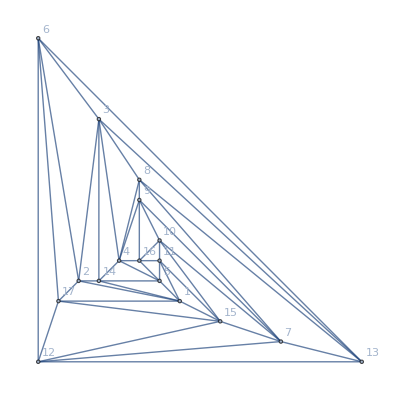

```mathematica
pl8=Graph[s3, VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
MaximalPlanarQ[pl8]
```

True

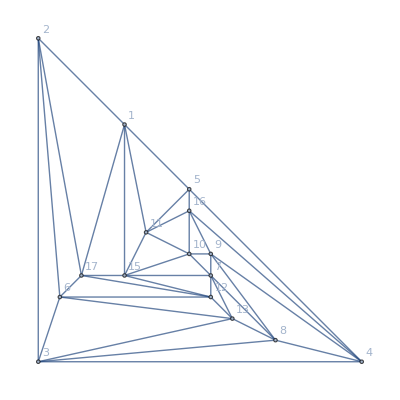

```mathematica
pl8Bis=VertexDelete[pl8,14]
```

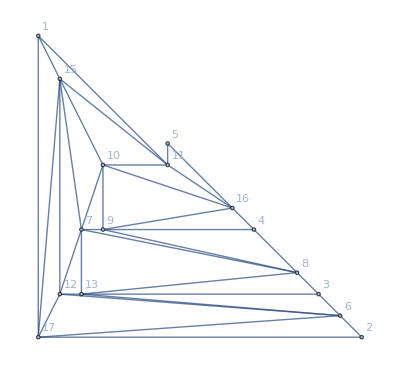

```mathematica
pl8Ter=EdgeDelete[pl8Bis,EdgeList[CycleGraph[5]]]
```

```mathematica
ChromaticPolynomial[pl8,x]==ChromaticPolynomial[Graph[plantri[[8]]],x]
```

True

```mathematica
ChromaticPolynomial[pl8,x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
ChromaticPolynomial[Graph[plantri[[8]]],x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
EmbedGraphInPlantri8Ter[key_]:=Block[{val=allGraphs5[key], sets, reference={12,13,7,15,17}, g, sub,edges},
sets=val["vertexsets"];
g=pl8Ter;
Table[If[Length[s]>1,
g=VertexContract[g,Sort[s]]
], {s,sets}];
sub=val["graph"];
edges=Map[First[sets[[#[[1]]]]]<-> First[sets[[#[[2]]]]]&,EdgeList[sub]];
g=EdgeAdd[g,edges];
Graph[VertexList[g],EdgeList[g],VertexLabels->Table[First[s]->Column[s],{s,sets}],GraphHighlight->edges]
]
```

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
EdgeList[allGraphs5[alfa1Key,"graph"]]
```

{1<->2,1<->3,2<->3}

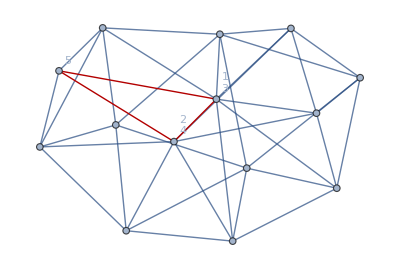

```mathematica
EmbedGraphInPlantri8Ter[alfa1Key]
```

```mathematica
Fulls=Association[]
```

<||>

```mathematica
Table[Fulls[k]=Association[],{k,Keys[allGraphs5]}];
```

```mathematica
Monitor[Table[Fulls[k,"graph"]=EmbedGraphInPlantri8Ter[k],{k,Keys[allGraphs5]}],k];
```

```mathematica
Monitor[Table[Fulls[k,"chromial"]=ChromaticPolynomial[Fulls[k,"graph"],x],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
Monitor[Table[Fulls[k,"coeff"]=CompleteBaseCoeff[Fulls[k,"chromial"]],{k,Sort[Keys[allGraphs5]]}],k];
```

$Aborted

```mathematica
EMptyBaseCoeff[poly_]:=PadRight[CoefficientList[poly,x],17,0]
```

```mathematica
EMptyBaseCoeff[Fulls[0,"chromial"]]
```

{0,-686808,4062732,-11179006,19059385,-22586469,19749882,-13182082,6843891,-2787401,890524,-221290,41986,-5885,575,-35,1}

```mathematica
Fulls[0,"chromial"]
```

-686808 x+4062732 x^2-11179006 x^3+19059385 x^4-22586469 x^5+19749882 x^6-13182082 x^7+6843891 x^8-2787401 x^9+890524 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16

```mathematica
Monitor[Table[Fulls[k,"coeffnull"]=EMptyBaseCoeff [Fulls[k,"chromial"]],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
Table[PadRight[Fulls[k,"coeff"],17],{k,allGraphs5AtomKeys}]//MatrixRank
```

13

```mathematica
Table[PadRight[Fulls[k,"coeff"],17]->CompleteBaseCoeff[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,amigos}]//Sort
```

{{0,0,0,0,23,16766,565003,4026884,10039735,11192632,6398336,2029888,372542,39965,2443,78,1}→{0,0,0,1,3,1},{0,0,0,0,27,16542,559967,4004628,10005251,11169846,6391218,2028802,372465,39963,2443,78,1}→{0,0,0,1,3,1},{0,0,0,0,27,16542,559967,4004628,10005251,11169846,6391218,2028802,372465,39963,2443,78,1}→{0,0,0,1,3,1},{0,0,0,0,34,17272,566279,4021619,10025513,11181710,6394752,2029335,372503,39964,2443,78,1}→{0,0,0,1,3,1},{0,0,0,0,34,17272,566279,4021619,10025513,11181710,6394752,2029335,372503,39964,2443,78,1}→{0,0,0,1,3,1}}

```mathematica
Prepend[Table[Indexed[a,k],{k,amigos}],v1x2x3x4x5]
```

{v1x2x3x4x5,a29413,a20773,a27229,a22933,a20695}

```mathematica
Reduce[
Fold[And,Table[Indexed[a,k]>0,{k,amigos}]]&&
Fold[And,Table[allGraphs5[k,"colofour"]>0,{k,quads}]]&&
Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,alfa1s}]]&&
Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,{K5Key}}]]&&
Fold[And,Table[(allGraphs5[k,"colofour"])==Indexed[a,k],{k,amigos}]]
,Append[Table[Indexed[a,k],{k,amigos}],v1x2x3x4x5]
,Integers]
```

(C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0&&v13x24x5==0&&v13x25x4==0&&v13x2x4x5==1+C[1]&&v14x25x3==0&&v14x2x35==0&&v14x2x3x5==1+C[2]&&v1x24x35==0&&v1x24x3x5==1+C[3]&&v1x25x3x4==1+C[4]&&v1x2x35x4==1+C[5]&&a29413==3+C[3]+C[4]+C[5]&&a20773==3+C[1]+C[2]+C[5]&&a27229==3+C[2]+C[3]+C[4]&&a22933==3+C[1]+C[4]+C[5]&&a20695==3+C[1]+C[2]+C[3]&&v1x2x3x4x5==0

```mathematica
rep5Show=Table[allGraphs5[k,"colofour"]->ShowGraph5Least[k],{k,allGraphs5AtomKeys}];
```

```mathematica
Table[allGraphs5[k,"colofour"]/.rep5Show,{k,amigos}]
```

{-Graphics-296080+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,-Graphics-317140+-Graphics-360850+-Graphics-317110+-Graphics-295270+-Graphics-295240,-Graphics-317380+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240,-Graphics-361120+-Graphics-360850+-Graphics-295510+-Graphics-295270+-Graphics-295240,-Graphics-361660+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295240}

```mathematica
Table[allGraphs5[k,"atleastwhy"],{k,amigos}]
```

{Comp is 'greater'.,Comp is 'greater'.,Comp is 'greater'.,Comp is 'greater'.,Comp is 'greater'.}

```mathematica
Table[allGraphs5[k,"atleast"],{k,amigos}]
```

{1,1,1,1,1}

```mathematica
Reduce[Table[(allGraphs5[k,"colofour"]/.{v1x2x3x4x5->0})==Indexed[a,k],{k,amigos}],Table[allGraphs5[m,"colofour"],{m,alfa1s}]]
```

v13x24x5==-v13x2x4x5-v14x2x3x5-v1x24x3x5+a20695&&v14x25x3==-v14x2x3x5-v1x24x3x5-v1x25x3x4+a27229&&v1x24x35==-v1x24x3x5-v1x25x3x4-v1x2x35x4+a29413&&v13x25x4==-v13x2x4x5-v1x25x3x4-v1x2x35x4+a22933&&v14x2x35==-v13x2x4x5-v14x2x3x5-v1x2x35x4+a20773

```mathematica
Reduce[Table[(allGraphs5[k,"colofour"]/.Table[allGraphs5[p,"colofour"]->0,{p,Append[alfa1s,K5Key]}])==Indexed[a,k],{k,amigos}],{v1x2x3x4x5,v14x25x3,v13x2x4x5,v13x25x4,v13x24x5}]
```

v1x2x35x4==-a20695/3+(2 a20773)/3-a22933/3-a27229/3+(2 a29413)/3&&v1x25x3x4==-a20695/3-a20773/3+(2 a22933)/3+(2 a27229)/3-a29413/3&&v1x24x3x5==(2 a20695)/3-a20773/3-a22933/3-a27229/3+(2 a29413)/3&&v14x2x3x5==-a20695/3+(2 a20773)/3-a22933/3+(2 a27229)/3-a29413/3&&v13x2x4x5==(2 a20695)/3-a20773/3+(2 a22933)/3-a27229/3-a29413/3

```mathematica
repJef=Solve[Table[(allGraphs5[k,"colofour"]/.Table[allGraphs5[p,"colofour"]->0,{p,Append[alfa1s,K5Key]}])==Indexed[a,k],{k,amigos}],Table[allGraphs5[k,"colofour"],{k,quads}]]
```

{{v13x2x4x5→1/3 (2 a20695-a20773+2 a22933-a27229-a29413),v1x24x3x5→1/3 (2 a20695-a20773-a22933-a27229+2 a29413),v1x2x35x4→1/3 (-a20695+2 a20773-a22933-a27229+2 a29413),v14x2x3x5→1/3 (-a20695+2 a20773-a22933+2 a27229-a29413),v1x25x3x4→1/3 (-a20695-a20773+2 a22933+2 a27229-a29413)}}

```mathematica
AmigoCoeff[form_]:=Table[Coefficient[form,k],{k,Table[Indexed[a,k],{k,amigos}]}]
```

```mathematica
AmigoCoeff[1/3 (2 a20695-a20773+2 a22933-a27229-a29413)]
```

{-1/3,-1/3,-1/3,2/3,2/3}

```mathematica
MatrixForm[3*Map[AmigoCoeff[#[[2]]]&,First[Solve[Table[(allGraphs5[k,"colofour"]/.Table[allGraphs5[p,"colofour"]->0,{p,Append[alfa1s,K5Key]}])==Indexed[a,k],{k,amigos}],Table[allGraphs5[k,"colofour"],{k,quads}]]]]].MatrixForm[Table[Fulls[k,"chromial"]/24/.x->4,{k,amigos}]]
```

(-1 | -1 | -1 | 2 | 2
2 | -1 | -1 | -1 | 2
2 | 2 | -1 | -1 | -1
-1 | 2 | 2 | -1 | -1
-1 | -1 | 2 | 2 | -1).(23
27
34
34
27)

```mathematica
(3*Map[AmigoCoeff[#[[2]]]&,First[Solve[Table[(allGraphs5[k,"colofour"]/.Table[allGraphs5[p,"colofour"]->0,{p,Append[alfa1s,K5Key]}])==Indexed[a,k],{k,amigos}],Table[allGraphs5[k,"colofour"],{k,quads}]]]]).(Table[Fulls[k,"chromial"]/24/.x->4,{k,amigos}])
```

{38,5,5,38,59}

```mathematica
Table[(allGraphs5[k,"colofour"]/.Table[allGraphs5[p,"colofour"]->0,{p,Append[alfa1s,K5Key]}])==Indexed[a,k],{k,amigos}]
```

{v1x24x3x5+v1x25x3x4+v1x2x35x4==a29413,v13x2x4x5+v14x2x3x5+v1x2x35x4==a20773,v14x2x3x5+v1x24x3x5+v1x25x3x4==a27229,v13x2x4x5+v1x25x3x4+v1x2x35x4==a22933,v13x2x4x5+v14x2x3x5+v1x24x3x5==a20695}

```mathematica
repCoeff=Table[allGraphs5[k,"colofour"]->PadRight[Fulls[k,"coeff"],17],{k,allGraphs5AtomKeys}];
```

```mathematica
Table[
Labeled[Framed[TableForm[Append[
Map[(#/.repCoeff)&,ListofVars[allGraphs5[k,"colofour"]]],
Map[Style[#,Darker[Green]]&,Fulls[k,"coeff"]]
],TableDepth->2,TableHeadings->{Append[ListofVars[allGraphs5[k,"colofour"]],k], None}]],ShowGraph[allGraphs5,k]],{k,amigos}]//Sort//TableForm
```

v1x24x35 | 0 | 0 | 0 | 0 | 0 | 1586 | 33088 | 146892 | 231967 | 163709 | 57997 | 10874 | 1080 | 53 | 1 | 0 | 0
v1x24x3x5 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x25x3x4 | 0 | 0 | 0 | 0 | 11 | 4136 | 108277 | 634418 | 1315458 | 1216259 | 569804 | 144977 | 20593 | 1610 | 64 | 1 | 0
v1x2x35x4 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x2x3x4x5 | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
29413 | 0 | 0 | 0 | 0 | 23 | 16766 | 565003 | 4026884 | 10039735 | 11192632 | 6398336 | 2029888 | 372542 | 39965 | 2443 | 78 | 1-Graphics-29413
v13x24x5 | 0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
v13x2x4x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v14x2x3x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v1x24x3x5 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x2x3x4x5 | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
20695 | 0 | 0 | 0 | 0 | 27 | 16542 | 559967 | 4004628 | 10005251 | 11169846 | 6391218 | 2028802 | 372465 | 39963 | 2443 | 78 | 1-Graphics-20695
v14x25x3 | 0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
v14x2x3x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v1x24x3x5 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x25x3x4 | 0 | 0 | 0 | 0 | 11 | 4136 | 108277 | 634418 | 1315458 | 1216259 | 569804 | 144977 | 20593 | 1610 | 64 | 1 | 0
v1x2x3x4x5 | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
27229 | 0 | 0 | 0 | 0 | 34 | 17272 | 566279 | 4021619 | 10025513 | 11181710 | 6394752 | 2029335 | 372503 | 39964 | 2443 | 78 | 1-Graphics-27229
v13x25x4 | 0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
v13x2x4x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v1x25x3x4 | 0 | 0 | 0 | 0 | 11 | 4136 | 108277 | 634418 | 1315458 | 1216259 | 569804 | 144977 | 20593 | 1610 | 64 | 1 | 0
v1x2x35x4 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x2x3x4x5 | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
22933 | 0 | 0 | 0 | 0 | 34 | 17272 | 566279 | 4021619 | 10025513 | 11181710 | 6394752 | 2029335 | 372503 | 39964 | 2443 | 78 | 1-Graphics-22933
v13x2x4x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v14x2x35 | 0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
v14x2x3x5 | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
v1x2x35x4 | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
v1x2x3x4x5 | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
20773 | 0 | 0 | 0 | 0 | 27 | 16542 | 559967 | 4004628 | 10005251 | 11169846 | 6391218 | 2028802 | 372465 | 39963 | 2443 | 78 | 1-Graphics-20773

```mathematica
Table[PadRight[Fulls[k,"coeff"],17]->CompleteBaseCoeff[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,quads}]//Sort
```

{{0,0,0,0,6,3551,103568,625157,1308956,1214382,569580,144968,20593,1610,64,1,0}→{0,0,0,0,1},{0,0,0,0,6,3551,103568,625157,1308956,1214382,569580,144968,20593,1610,64,1,0}→{0,0,0,0,1},{0,0,0,0,9,3696,103438,619374,1296107,1204556,566279,144444,20555,1609,64,1,0}→{0,0,0,0,1},{0,0,0,0,9,3696,103438,619374,1296107,1204556,566279,144444,20555,1609,64,1,0}→{0,0,0,0,1},{0,0,0,0,11,4136,108277,634418,1315458,1216259,569804,144977,20593,1610,64,1,0}→{0,0,0,0,1}}

```mathematica
Table[PadRight[Fulls[k,"coeff"],17]->CompleteBaseCoeff[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,alfa1s}]//Sort//TableForm
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1,0,0}→{0,0,0,1}
{0,0,0,0,3,1657,33021,145463,229683,162452,57705,10845,1079,53,1,0,0}→{0,0,0,1}
{0,0,0,0,3,1657,33021,145463,229683,162452,57705,10845,1079,53,1,0,0}→{0,0,0,1}
{0,0,0,0,8,1947,34494,147410,230594,162613,57714,10845,1079,53,1,0,0}→{0,0,0,1}
{0,0,0,0,8,1947,34494,147410,230594,162613,57714,10845,1079,53,1,0,0}→{0,0,0,1}

```mathematica
Table[PadRight[Fulls[k,"coeff"],17],{k,allGraphs5AtomKeys}]//Sort//TableForm
```

0 | 0 | 0 | 0 | 0 | 1586 | 33088 | 146892 | 231967 | 163709 | 57997 | 10874 | 1080 | 53 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1
0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 760 | 10232 | 32749 | 38561 | 20357 | 5286 | 691 | 43 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 760 | 10232 | 32749 | 38561 | 20357 | 5286 | 691 | 43 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 757 | 10191 | 32720 | 38557 | 20357 | 5286 | 691 | 43 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 757 | 10191 | 32720 | 38557 | 20357 | 5286 | 691 | 43 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
0 | 0 | 0 | 0 | 7 | 2392 | 41877 | 172657 | 261609 | 179637 | 62319 | 11474 | 1120 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 2284 | 41654 | 173601 | 263584 | 180822 | 62606 | 11503 | 1121 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 2284 | 41654 | 173601 | 263584 | 180822 | 62606 | 11503 | 1121 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 2361 | 42259 | 175838 | 266416 | 182246 | 62920 | 11533 | 1122 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 8 | 2361 | 42259 | 175838 | 266416 | 182246 | 62920 | 11533 | 1122 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 9 | 856 | 10460 | 32686 | 38275 | 20222 | 5265 | 690 | 43 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
0 | 0 | 0 | 0 | 10 | 2495 | 42916 | 176799 | 267027 | 182426 | 62943 | 11534 | 1122 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 10 | 2495 | 42916 | 176799 | 267027 | 182426 | 62943 | 11534 | 1122 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 10 | 5000 | 131141 | 748574 | 1508903 | 1359624 | 622516 | 155160 | 21630 | 1662 | 65 | 1 | 0
0 | 0 | 0 | 0 | 10 | 5000 | 131141 | 748574 | 1508903 | 1359624 | 622516 | 155160 | 21630 | 1662 | 65 | 1 | 0
0 | 0 | 0 | 0 | 11 | 1376 | 16034 | 46533 | 50629 | 24993 | 6120 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 11 | 1426 | 16203 | 46597 | 50598 | 24980 | 6119 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 11 | 1426 | 16203 | 46597 | 50598 | 24980 | 6119 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 11 | 4136 | 108277 | 634418 | 1315458 | 1216259 | 569804 | 144977 | 20593 | 1610 | 64 | 1 | 0
0 | 0 | 0 | 0 | 11 | 5143 | 132271 | 750663 | 1510322 | 1360031 | 622565 | 155162 | 21630 | 1662 | 65 | 1 | 0
0 | 0 | 0 | 0 | 11 | 5143 | 132271 | 750663 | 1510322 | 1360031 | 622565 | 155162 | 21630 | 1662 | 65 | 1 | 0
0 | 0 | 0 | 0 | 12 | 1516 | 16790 | 47390 | 50951 | 25038 | 6122 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12 | 1516 | 16790 | 47390 | 50951 | 25038 | 6122 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 13 | 2481 | 42497 | 174810 | 264339 | 181033 | 62631 | 11504 | 1121 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 13 | 2481 | 42497 | 174810 | 264339 | 181033 | 62631 | 11504 | 1121 | 54 | 1 | 0 | 0
0 | 0 | 0 | 0 | 14 | 3175 | 52880 | 209220 | 305295 | 202659 | 68209 | 12224 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 14 | 3255 | 53148 | 209548 | 305588 | 202783 | 68229 | 12225 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 14 | 3255 | 53148 | 209548 | 305588 | 202783 | 68229 | 12225 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 16 | 800 | 5369 | 10435 | 8024 | 2810 | 470 | 36 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16 | 1616 | 16907 | 47109 | 50555 | 24884 | 6100 | 758 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16 | 1616 | 16907 | 47109 | 50555 | 24884 | 6100 | 758 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16 | 3293 | 53373 | 209793 | 305537 | 202698 | 68211 | 12224 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 16 | 3293 | 53373 | 209793 | 305537 | 202698 | 68211 | 12224 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 18 | 1610 | 17026 | 47626 | 51054 | 25056 | 6123 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 1610 | 17026 | 47626 | 51054 | 25056 | 6123 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 20 | 3640 | 55771 | 214119 | 308453 | 203528 | 68310 | 12228 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 20 | 3640 | 55771 | 214119 | 308453 | 203528 | 68310 | 12228 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 20 | 5638 | 135388 | 756581 | 1515037 | 1361848 | 622913 | 155193 | 21631 | 1662 | 65 | 1 | 0
0 | 0 | 0 | 0 | 21 | 3508 | 54096 | 210431 | 305740 | 202723 | 68212 | 12224 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 26 | 1651 | 16785 | 47020 | 50699 | 24987 | 6119 | 759 | 45 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 29 | 3670 | 54950 | 211758 | 306547 | 202939 | 68237 | 12225 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 29 | 3670 | 54950 | 211758 | 306547 | 202939 | 68237 | 12225 | 1165 | 55 | 1 | 0 | 0
0 | 0 | 0 | 0 | 31 | 2994 | 45012 | 179330 | 268115 | 182602 | 62952 | 11534 | 1122 | 54 | 1 | 0 | 0